## formula definitions

```mathematica
JoinGraphs2[with_,without_,contract_]:=Block [{edges,full,
edgef=EdgeList[with],
edgeg=EdgeList[without],
edgeh=EdgeList[contract],
greenEdges,
blueEdges,
greenStarts,
blueToGreen=Association[] (* gives for each blue (contract) vertex a vertex in the "with" graph *),
orangeEgdes
},
(* greenedges are the ones connecting the with with the contract So each green starts in the "with" and ends
   in the "contract" *)
greenEdges=SetDifference[SetDifference[edgeg,edgef],edgeh];
greenStarts=Map[(blueToGreen[#[[2]]]=#[[1]];#[[1]])&,greenEdges];
blueEdges=edgeh;
edges=Join[
Table[e->Directive[{Red}],{e,edgef}],
Table[e->Directive[{Thickness[0.02],Darker[Green]}],{e,greenEdges}],
Table[e->Directive[{Blue}],{e,blueEdges}]
];
orangeEgdes=Map[blueToGreen[#[[1]]]->blueToGreen[#[[2]]]&,blueEdges];
(* rewrite the orange edges *)
edges=Table[If[MemberQ[orangeEgdes,edge[[1]]],edge[[1]]->Directive[{Thickness[0.02],Orange}],edge],{edge,edges}];

(* now combine the graphs and emit*)
full=GraphUnion[with,without,contract];
(*full=Graph[VertexList[full],MapAll[SortEdge,EdgeList[full]]];*)
Graph[VertexList[full],EdgeList[full],VertexLabels->Table[v->If[SymbolLevel[v]==4,Rotate[Framed[SymbolToLabel2[v],FrameStyle->If[VertexQ[contract,v],Directive[Blue,Dashed],Directive[Red,Thickness[0.001]]]],Pi/4],Rotate[SymbolToLabel2[v],Pi/4]],{v,VertexList[full]}],EdgeStyle->edges,
VertexStyle->Join[
Table[v->Red,{v,VertexList[with]}],
Table[v->Blue,{v,VertexList[contract]}]],
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->400
]
]
```

```mathematica
DrawWithWithoutAndContract2[g_]:=Block[{edges,full,implied={},mpg},
edges=EdgeList[GraphComplement[g]];
mpg=CollectMPGEdges[g];
Monitor[
{
Labeled[
Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],
Map[With[{s=#},If[SymbolLevel[s]==4,Framed[SymbolToLabel2[s]],SymbolToLabel2[s]]]&,FindFullFormula[g]]]
,
Table[With[{
without=Graph[g,VertexLabels->"Name",GraphHighlight->{e[[1]],e[[2]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding", ImageSize->40],
contract =Graph[GContract[g,e],VertexLabels->"Name",GraphHighlight->{e[[1]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding", ImageSize->40],
with=Graph[EdgeAdd[g,e],GraphHighlight->e,GraphLayout->"TutteEmbedding", VertexLabels->"Name",GraphHighlightStyle->"Thick", ImageSize->40]
},
With[
{ffull=FindFullFormula[with],
fwithout=FindFullFormula[without],
fcontract=Map[SymbolReplace[#,e]&,FindFullFormula[contract]]
},
implied=Join[implied,ImpliedNodes[fcontract,ffull]];
Labeled[
Graph[
JoinGraphs2[
FormulaGraphReverse2[ffull],
FormulaGraphReverse2[fwithout],
FormulaGraphReverse2[fcontract]
], ImageSize->300, AspectRatio->1/GoldenRatio
],
{If[MemberQ[mpg,e],Style[e,Red],e],Map[SymbolToLabel2,fcontract]}]
]
],{e,Sort[Map[SortEdge,edges]]}]},
e]
]
```

## Experiments w

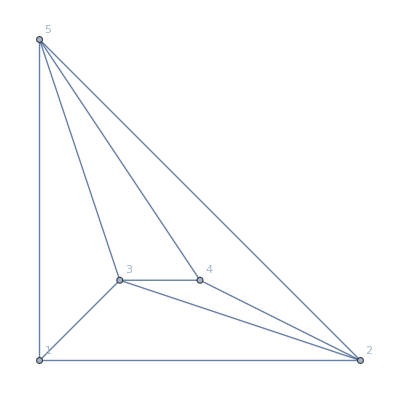
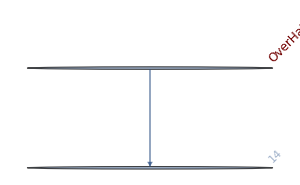
{-Graphics-{OverHat[1],14},{-Graphics-{1<->4,{14}}}}

```mathematica
DrawWithWithoutAndContract2[ReadGrof[2]]
```

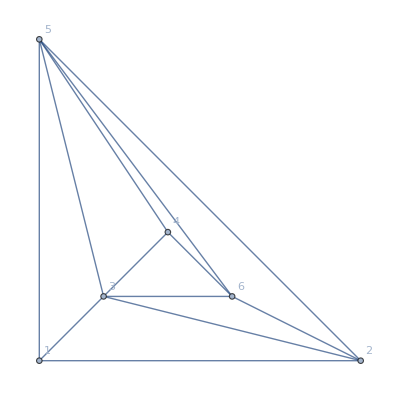
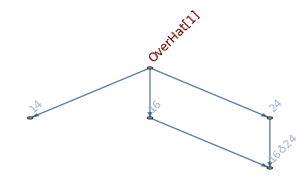
{-Graphics-{OverHat[1],24,14,16,16♁24},{-Graphics-{1<->4,{14}},-Graphics-{1<->6,{16,16♁24}},-Graphics-{2<->4,{24,16♁24}}}}

```mathematica
DrawWithWithoutAndContract2[ReadGrof[3]]
```

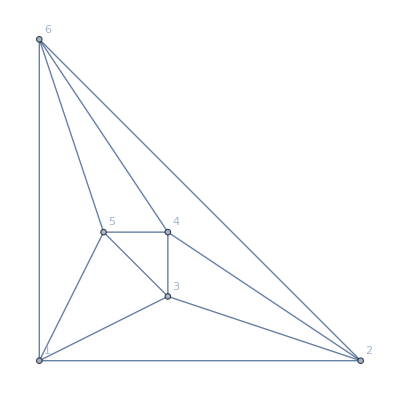
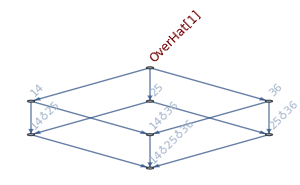
{-Graphics-{OverHat[1],36,25,25♁36,14,14♁36,14♁25,14♁25♁36},{-Graphics-{1<->4,{14,14♁36,14♁25,14♁25♁36}},-Graphics-{2<->5,{25,25♁36,14♁25,14♁25♁36}},-Graphics-{3<->6,{36,25♁36,14♁36,14♁25♁36}}}}

```mathematica
DrawWithWithoutAndContract2[ReadGrof[4]]
```

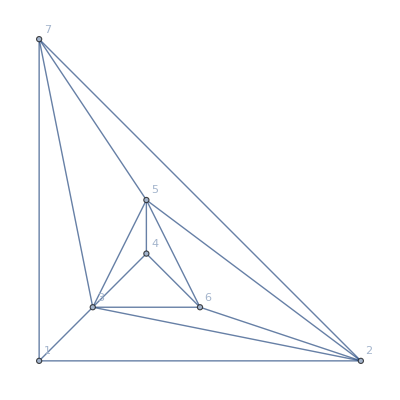
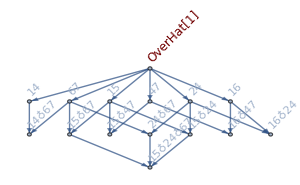
{-Graphics-{OverHat[1],47,67,24,24♁67,14,14♁67,16,16♁47,16♁24,15,15♁47,15♁67,15♁24,15♁24♁67},{-Graphics-{1<->4,{14,14♁67}},-Graphics-{1<->5,{15,15♁47,15♁67,15♁24,15♁24♁67}},-Graphics-{1<->6,{16,16♁47,16♁24}},-Graphics-{2<->4,{24,24♁67,16♁24,15♁24,15♁24♁67}},-Graphics-{4<->7,{47,16♁47,15♁47}},-Graphics-{6<->7,{67,24♁67,14♁67,15♁67,15♁24♁67}}}}

```mathematica
DrawWithWithoutAndContract2[ReadGrof[5]]
```

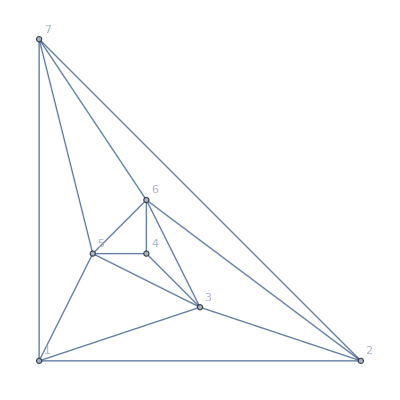
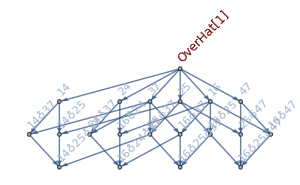
{-Graphics-{OverHat[1],47,37,24,24♁37,25,25♁47,25♁37,14,14♁37,14♁25,14♁25♁37,16,16♁47,16♁37,16♁24,16♁24♁37,16♁25,16♁25♁47,16♁25♁37},{-Graphics-{1<->4,{14,14♁37,14♁25,14♁25♁37}},-Graphics-{1<->6,{16,16♁47,16♁37,16♁24,16♁24♁37,16♁25,16♁25♁47,16♁25♁37}},-Graphics-{2<->4,{24,24♁37,16♁24,16♁24♁37}},-Graphics-{2<->5,{25,25♁47,25♁37,14♁25,14♁25♁37,16♁25,16♁25♁47,16♁25♁37}},-Graphics-{3<->7,{37,24♁37,25♁37,14♁37,14♁25♁37,16♁37,16♁24♁37,16♁25♁37}},-Graphics-{4<->7,{47,25♁47,16♁47,16♁25♁47}}}}

```mathematica
DrawWithWithoutAndContract2[ReadGrof[6]]
```